```mathematica
DistMoments = (FullSimplify[{ap/(mp*(ap-1)),ap^3/(mp^2*(ap-1)^2*(ap-2))}/.{mp->m/n,ap->a*n^(ζ-2)}])/.m->ρ*μ*(1/β)
```

{-(a n^(1+ζ))/((n^2 μ ρ)/β-(a n^ζ μ ρ)/β),(a^3 n^(-4+3 ζ) β^2)/((-2+a n^(-2+ζ)) (-1+a n^(-2+ζ))^2 μ^2 ρ^2)}

Introduce the following allometric relationships
(Population size from Damuth) n -> (0.0116)*M^-0.776
(β grams/bitesize) β = (0.002 *(masskg)^0.969) =2.47759×10^-6 M^0.969
(Resource density) μ ->
(Dispersion) alpha ->

```mathematica
ScaledDistMoments = FullSimplify[DistMoments/.n->n0*M^(-eta)]
```

{-((a M^eta n0 (M^-eta n0)^ζ β)/(n0^2 μ ρ-a M^(2 eta) (M^-eta n0)^ζ μ ρ)),(a^3 (M^-eta n0)^(-4+3 ζ) β^2)/((-2+a (M^-eta n0)^(-2+ζ)) (-1+a (M^-eta n0)^(-2+ζ))^2 μ^2 ρ^2)}

```mathematica
DistExp = ScaledDistMoments[[1]];
DistVar = ScaledDistMoments[[2]];
```

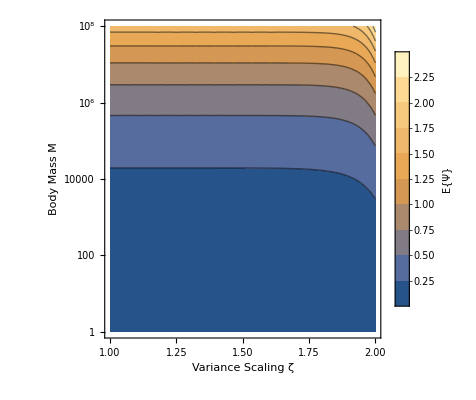

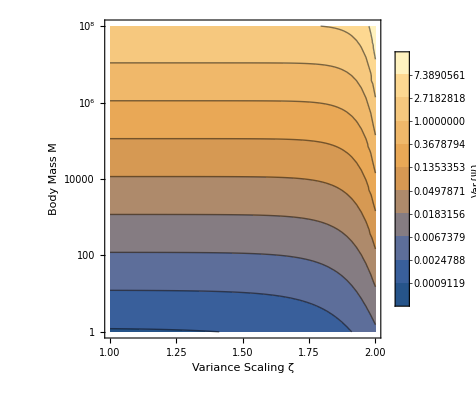

```mathematica
ContourPlot[DistExp/.{n0->0.0116,eta->3/4,β->2.4775931730607385*^-6 M^0.969,ρ->1,μ->0.000001,a->3},{ζ,1,2},{M,1,1*10^8},ScalingFunctions->{None,"Log"},PlotRange->All,FrameLabel->{"Variance Scaling ζ","Body Mass M"},PlotLegends->BarLegend[Automatic,LegendLabel->"E{Ψ}"]]
ContourPlot[DistVar/.{n0->0.0116,eta->3/4,β->2.4775931730607385*^-6 M^0.969,ρ->1,μ->0.000001,a->3},{ζ,1,2},{M,1,1*10^8},ScalingFunctions->{None,"Log","Log"},PlotRange->All,FrameLabel->{"Variance Scaling ζ","Body Mass M"},PlotLegends->BarLegend[Automatic,LegendLabel->"Var{Ψ}"]]
```

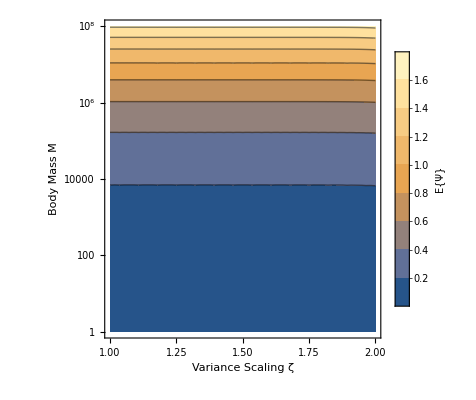

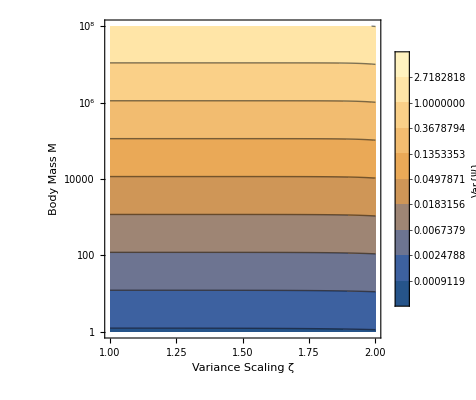

```mathematica
ContourPlot[DistExp/.{n0->0.0116,eta->3/4,β->2.4775931730607385*^-6 M^0.969,ρ->1,μ->0.000001,a->100},{ζ,1,2},{M,1,1*10^8},ScalingFunctions->{None,"Log"},PlotRange->All,FrameLabel->{"Variance Scaling ζ","Body Mass M"},PlotLegends->BarLegend[Automatic,LegendLabel->"E{Ψ}"]]
ContourPlot[DistVar/.{n0->0.0116,eta->3/4,β->2.4775931730607385*^-6 M^0.969,ρ->1,μ->0.000001,a->100},{ζ,1,2},{M,1,1*10^8},ScalingFunctions->{None,"Log","Log"},PlotRange->All,FrameLabel->{"Variance Scaling ζ","Body Mass M"},PlotLegends->BarLegend[Automatic,LegendLabel->"Var{Ψ}"]]
```